# ApplyPauliTransferMap

```mathematica
SetDirectory @ NotebookDirectory[];
Import["../Link/QuESTlink.m"];
```

## Doc

```mathematica
?ApplyPauliTransferMap
```

## Correctness

## Maps

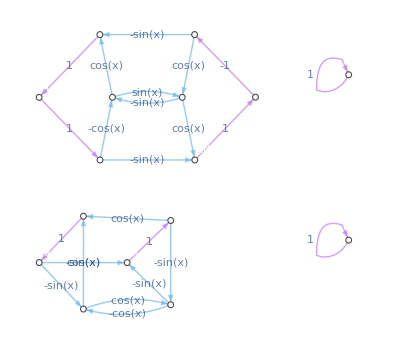

```mathematica
map = CalcPauliTransferMap @ Circuit[Subscript[H, 0] Subscript[Rx, 0][x]Subscript[C, 0][Subscript[X, 1]]];
DrawPauliTransferMap[map]
```

```mathematica
ApplyPauliTransferMap[Subscript[X, 1] Subscript[Z, 0], map]
```

X_0

```mathematica
ApplyPauliTransferMap[a Subscript[X, 0] Subscript[Z, 1] + b Subscript[X, 1] + c Subscript[X, 1] Subscript[Z, 0], map]
```

c X_0+b X_1-a Sin[x] X_0 Y_1+a Cos[x] Z_1

```mathematica
ApplyPauliTransferMap[a Subscript[X, 0] Subscript[Z, 1] + b Subscript[X, 1] + c Subscript[X, 1] Subscript[Z, 0], {map,map,map,map,map,map, map}]
```

-1/2 c (1+3 Cos[2 x]) Sin[x]^2 X_0+b X_1+c Cos[x]^5 X_0 X_1+c Cos[x] Sin[x] (Cos[x]^2+Cos[x]^4-2 Sin[x]^2) Y_0+c Cos[x]^2 (-1+2 Cos[2 x]) Sin[x] X_1 Y_0+a Sin[x] (-Cos[x]^2+Sin[x]^6-Sin[2 x]^2) X_0 Y_1-1/8 a Cos[x] (3-12 Cos[2 x]+Cos[4 x]) Y_0 Y_1+1/2 c Sin[x] Sin[4 x] Z_0+c Cos[x]^2 (3+Cos[x]^2) Sin[x]^2 X_1 Z_0-1/16 a (-1-16 Cos[2 x]+Cos[4 x]) Sin[2 x] Y_1 Z_0-1/8 a Cos[x] (3-20 Cos[2 x]+Cos[4 x]) Sin[x]^2 Z_1

```mathematica
4 ^ 2
str = Subscript[Z, 0]+Subscript[Y, 1];
Table[
	Length @ ApplyPauliTransferMap[str,ConstantArray[map,reps]],
	{reps,1,10}]
```

16

{2,3,5,8,10,10,10,10,10,10}

## Circuits

```mathematica
ApplyPauliTransferMap[a Subscript[X, 0] Subscript[Z, 1] + b Subscript[X, 1] + c Subscript[X, 1] Subscript[Z, 0], {map,Subscript[C, 0][Subscript[X, 1]], Subscript[PTM, 0]@DiagonalMatrix@{a,b,c,d}}]
```

a b X_1+b c X_0 X_1-a c Sin[x] Y_0 Z_1+a d Cos[x] Z_0 Z_1

```mathematica
n = 4;
u = GetKnownCircuit["QFT", n];
m = CalcCircuitMatrix[u];

ρin = RandomComplex[{-1-ⅈ,1+ⅈ}, {2^n, 2^n}];
ρout = m . ρin . ConjugateTranspose[m];

σin = GetPauliString[ρin];
σout = ApplyPauliTransferMap[σin, u];

CalcPauliExpressionMatrix[σout] - ρout // Abs // Max
```

5.68989×10^-16

## Options

### Caching

```mathematica
circ = Table[Subscript[C, 0][Subscript[X, 1]], 500];
Timing @ ApplyPauliTransferMap[a Subscript[X, 0] Subscript[Z, 1] + b Subscript[X, 1] + c Subscript[X, 1] Subscript[Z, 0] + Subscript[Y, 2], circ, "CacheMaps"->"Never"]
Timing @ ApplyPauliTransferMap[a Subscript[X, 0] Subscript[Z, 1] + b Subscript[X, 1] + c Subscript[X, 1] Subscript[Z, 0] + Subscript[Y, 2], circ, "CacheMaps"->"Forever"]
```

{3.38206,b X_1+Y_2+c X_1 Z_0+a X_0 Z_1}

{0.535208,b X_1+Y_2+c X_1 Z_0+a X_0 Z_1}

```mathematica
ApplyPauliTransferMap[a Subscript[X, 0] Subscript[Z, 1] + b Subscript[X, 1] + c Subscript[X, 1] Subscript[Z, 0] + Subscript[Y, 2], circ, "CacheMaps"->"Forever"];
DownValues[QuEST`Private`obtainCachedPTMap] // First

ApplyPauliTransferMap[a Subscript[X, 0] Subscript[Z, 1] + b Subscript[X, 1] + c Subscript[X, 1] Subscript[Z, 0] + Subscript[Y, 2], circ, "CacheMaps"->"Never"];
DownValues[QuEST`Private`obtainCachedPTMap] // First

ApplyPauliTransferMap[a Subscript[X, 0] Subscript[Z, 1] + b Subscript[X, 1] + c Subscript[X, 1] Subscript[Z, 0] + Subscript[Y, 2], circ, "CacheMaps"->"UntilCallEnd"];
DownValues[QuEST`Private`obtainCachedPTMap] // First
```

HoldPattern[QuEST`Private`obtainCachedPTMap[{C_1[X_0]},CacheMaps→Forever]]:>PTMap_(0,1)[0→{{0,1}},1→{{1,1}},2→{{14,1}},3→{{15,1}},4→{{5,1}},5→{{4,1}},6→{{11,1}},7→{{10,-1}},8→{{9,1}},9→{{8,1}},10→{{7,-1}},11→{{6,1}},12→{{12,1}},13→{{13,1}},14→{{2,1}},15→{{3,1}}]

HoldPattern[QuEST`Private`obtainCachedPTMap[QuEST`Private`compGate_,QuEST`Private`opts___]]:>(QuEST`Private`obtainCachedPTMap[QuEST`Private`compGate,QuEST`Private`opts]=CalcPauliTransferMap[QuEST`Private`compGate,Sequence@@FilterRules[{QuEST`Private`opts},Options[CalcPauliTransferMap]]])

HoldPattern[QuEST`Private`obtainCachedPTMap[QuEST`Private`compGate_,QuEST`Private`opts___]]:>(QuEST`Private`obtainCachedPTMap[QuEST`Private`compGate,QuEST`Private`opts]=CalcPauliTransferMap[QuEST`Private`compGate,Sequence@@FilterRules[{QuEST`Private`opts},Options[CalcPauliTransferMap]]])

### AssertValidChannels

```mathematica
ApplyPauliTransferMap[Subscript[X, 0] Subscript[Y, 1], Subscript[Depol, 0,1][x]]
ApplyPauliTransferMap[Subscript[X, 0] Subscript[Y, 1], Subscript[Depol, 0,1][x], AssertValidChannels->False]
```

1/15 (15-16 x) X_0 Y_1

1/15 (15 √(1-x) Conjugate[√(1-x)]-√x Conjugate[√x]) X_0 Y_1

## Errors

```mathematica
ApplyPauliTransferMap[Subscript[X, 0], {Subscript[blob, 0]}]
```

ApplyPauliTransferMap::error: Could not pre-compute the Pauli transfer maps due to the below error:

CalcPauliTransferMatrix::error: Circuit contained an unrecognised or unsupported gate: blob_0

$Failed

```mathematica
ApplyPauliTransferMap[Subscript[X, 0], Subscript[X, 0], "CacheMaps"->"Spaghetti"]
ApplyPauliTransferMap[Subscript[X, 0], {Subscript[X, 0]}, "CacheMaps"->"Spaghetti"]
ApplyPauliTransferMap[Subscript[X, 0], Subscript[PTM, 0][x], "CacheMaps"->"Spaghetti"]
ApplyPauliTransferMap[Subscript[X, 0], {Subscript[PTM, 0][x]}, "CacheMaps"->"Spaghetti"]
ApplyPauliTransferMap[Subscript[X, 0], Subscript[PTMap, 0][x], "CacheMaps"->"Spaghetti"]
ApplyPauliTransferMap[Subscript[X, 0], {Subscript[PTMap, 0][x]}, "CacheMaps"->"Spaghetti"]
```

ApplyPauliTransferMap::error: Option "CacheMaps" must be one of "Forever", "UntilCallEnd" or "Never".

$Failed

ApplyPauliTransferMap::error: Option "CacheMaps" must be one of "Forever", "UntilCallEnd" or "Never".

$Failed

ApplyPauliTransferMap::error: Option "CacheMaps" must be one of "Forever", "UntilCallEnd" or "Never".

$Failed

ApplyPauliTransferMap::error: Option "CacheMaps" must be one of "Forever", "UntilCallEnd" or "Never".

$Failed

ApplyPauliTransferMap::error: Option "CacheMaps" must be one of "Forever", "UntilCallEnd" or "Never".

$Failed

ApplyPauliTransferMap::error: Option "CacheMaps" must be one of "Forever", "UntilCallEnd" or "Never".

$Failed

```mathematica
ApplyPauliTransferMap[Subscript[X, 0], {Subscript[X, 0]}, "BadOption"->True]
```

OptionValue::nodef: Unknown option BadOption for {CalcPauliTransferMap,ApplyPauliTransferMap,CalcPauliTransferEval}.

$Failed

```mathematica
ApplyPauliTransferMap[Subscript[X, 0], {Subscript[X, 0]}, "CombineStates"->"Only valid for CalcPauliTransferEval"]
```

OptionValue::nodef: Unknown option CombineStates for {CalcPauliTransferMap,ApplyPauliTransferMap}.

$Failed

```mathematica
ApplyPauliTransferMap[a, {Subscript[H, 0]}]
ApplyPauliTransferMap[Subscript[X, -1], {Subscript[H, 0]}]
ApplyPauliTransferMap[Subscript[X, 0] Subscript[X, 0], {Subscript[H, 0]}]
ApplyPauliTransferMap[Subscript[X, 0] Subscript[Y, 0], {Subscript[H, 0]}]
```

ApplyPauliTransferMap::error: Invalid arguments. See ?ApplyPauliTransferMap

$Failed

ApplyPauliTransferMap::error: Invalid arguments. See ?ApplyPauliTransferMap

$Failed

ApplyPauliTransferMap::error: Invalid arguments. See ?ApplyPauliTransferMap

$Failed

ApplyPauliTransferMap::error: Invalid arguments. See ?ApplyPauliTransferMap

$Failed